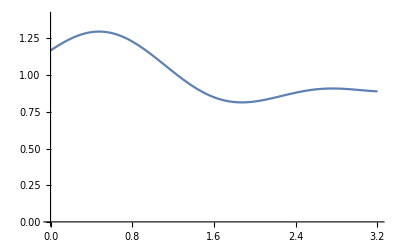

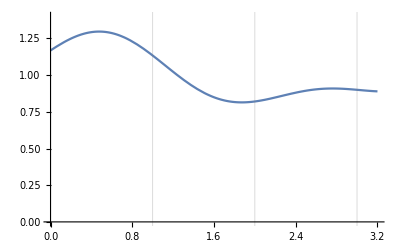

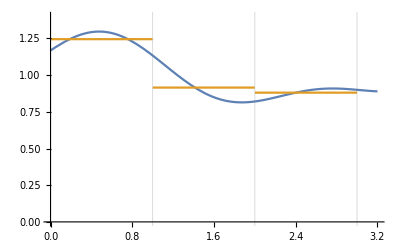

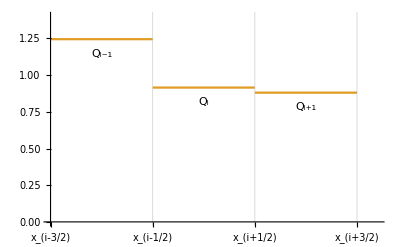

```mathematica
ClearAll[i,f,fpc]
$PrePrint=RawBoxes[ToBoxes[#]//.FractionBox[x_,y_]:>RowBox[{If[Head[x]===RowBox,RowBox[{"(",x,")"}],x],"/",If[Head[y]===RowBox,RowBox[{"(",y,")"}],y]}]]&;
f=1+.2Sin[1.5x+1]+0.1Sin[3x];
Plot[f,{x,0,3.2},PlotRange->{{0,3.2},{0,1.4}}]
Plot[f,{x,0,3.2},PlotRange->{{0,3.2},{0,1.4}},GridLines->{{1,2,3},{}}]
fpc=Piecewise[{Integrate[f,{x,##}],x<#2}&@@@Partition[Range@4-1,2,1],Null];
Plot[{f,fpc},{x,0,3.2},PlotRange->{{0,3.2},{0,1.4}},GridLines->{{1,2,3},{}}]
Show[Plot[{,fpc},{x,0,3.2},PlotRange->{{0,3.2},{0,1.4}},GridLines->{{1,2,3},{}},Ticks->{{{0,Subscript[x, i-3/2]},{0.5,Subscript[x, i-1],0},{1,Subscript[x, i-1/2]},{1.5,Subscript[x, i],0},{2,Subscript[x, i+1/2]},{2.5,Subscript[x, i+1],0},{3,Subscript[x, i+3/2]}},Automatic}],Graphics[Array[Text[Subscript[Q, i+#-2],{#-.5,fpc-.1/.x->#-.5}]&,3]]]
```

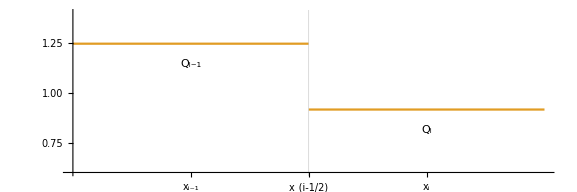

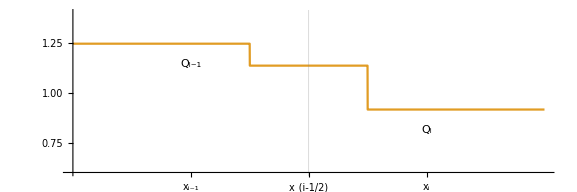

```mathematica
Show[Plot[{,fpc},{x,0,2},PlotRange->{{0,2},{.6,1.4}},GridLines->{{1},{}},Ticks->{{{0.5,Subscript[x, i-1],0},{1,Subscript[x, i-1/2]},{1.5,Subscript[x, i],0}},Automatic},AspectRatio->1/3],Graphics[Array[Text[Subscript[Q, i+#-2],{#-.5,fpc-.1/.x->#-.5}]&,2]]]
Show[Plot[{,Piecewise[{{fpc/.x->.5,y<.75},{fpc/.x->1.5,y>1.25}},((fpc/.x->.5)2+(fpc/.x->1.5))/3]},{y,0,2},PlotRange->{{0,2},{.6,1.4}},GridLines->{{1},{}},Ticks->{{{0.5,Subscript[x, i-1],0},{1,Subscript[x, i-1/2]},{1.5,Subscript[x, i],0}},Automatic},AspectRatio->1/3],Graphics[Array[Text[Subscript[Q, i+#-2],{#-.5,fpc-.1/.x->#-.5}]&,2]]]
```

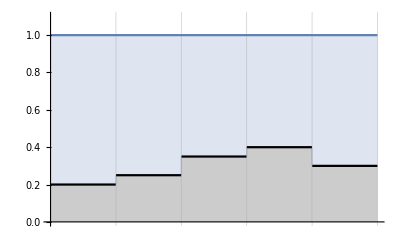

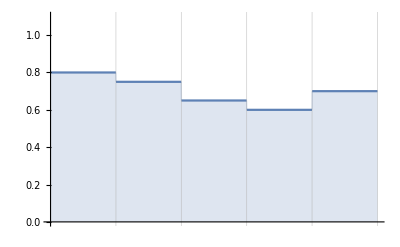

```mathematica
bathymetry=Piecewise[{{0.2,x<1},{0.25,x<2},{0.35,x<3},{0.4,x<4},{0.3,x<5}}];
Plot[{1,bathymetry},{x,0,5},PlotRange->{0,1.1},GridLines->{Range@5,{}},Ticks->{None,Automatic},PlotStyle->{Automatic,Black},Filling->{1->{2},2->Axis}]
Plot[1-bathymetry,{x,0,5},PlotRange->{0,1.1},GridLines->{Range@5,{}},Ticks->{None,Automatic},Filling->{1->Axis}]
```

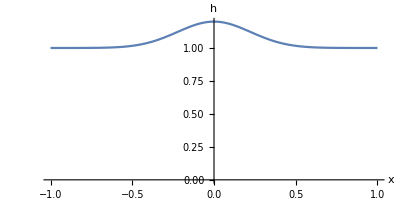

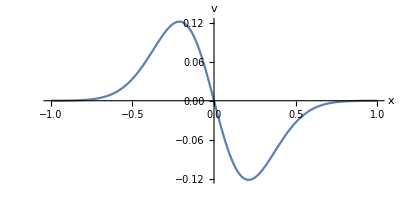

```mathematica
geo[x_]:=1+0.2Exp[-10x^2]
Plot[geo@x,{x,-1,1},PlotRange->{0,1.2},AspectRatio->1/2,AxesLabel->{x,h}]
Plot[geo'[x]geo@x/5,{x,-1,1},AspectRatio->1/2,AxesLabel->{x,v}]
```

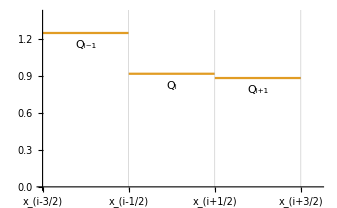

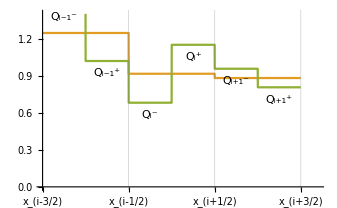

```mathematica
fpcLev=fpc+Piecewise[Join@@((r=#;{{#,x<r-.5},{-#,x<r}}&@RandomReal[{-.3,.3}])&/@Range@3)];
Show[Plot[{,fpc},{x,0,3.2},PlotRange->{{0,3.2},{0,1.4}},GridLines->{{1,2,3},{}},Ticks->{{{0,Subscript[x, i-3/2]},{0.5,Subscript[x, i-1],0},{1,Subscript[x, i-1/2]},{1.5,Subscript[x, i],0},{2,Subscript[x, i+1/2]},{2.5,Subscript[x, i+1],0},{3,Subscript[x, i+3/2]}},Automatic}],Graphics[Array[Text[Subscript[Q, i+#-2],{#-.5,fpc-.1/.x->#-.5}]&,3]]]
Show[Plot[{,fpc,fpcLev},{x,0,3.2},PlotRange->{{0,3.2},{0,1.4}},GridLines->{{1,2,3},{}},Ticks->{{{0,Subscript[x, i-3/2]},{0.5,Subscript[x, i-1],0},{1,Subscript[x, i-1/2]},{1.5,Subscript[x, i],0},{2,Subscript[x, i+1/2]},{2.5,Subscript[x, i+1],0},{3,Subscript[x, i+3/2]}},Automatic},Exclusions->None],Graphics[Array[{Text[Subscript[Q, i+#-2]^("-"),{#-.75,fpcLev-.1/.x->#-.75}],Text[Subscript[Q, i+#-2]^("+"),{#-.25,fpcLev-.1/.x->#-.25}]}&,3]]]
```